## Trompo de Kovalevskaya

#### Jhoan Camilo Eusse Kevin Cortés

junio 2020

El problema del movimiento de un cuerpo rígido con uno de sus puntos fijo, y bajo un campo gravitacional, es en general no soluble por cuadraturas. En 1888 Sofía Kovalevskya encontró una solución para este problema cuando los momentos principales de inercia EN EL PUNTO FIJO cumplen la relación:, y ademas el centro de masa del cuerpo debe estar en el plano formado por los ejes principales cuyos momentos de inercia son iguales.  
Se escoge el punto fijo O como origen tanto del sistema de coordenadas móviles (x1, x2, x3)  fijo al cuerpo, como para el sistema de coordenadas (X,Y,Z) del laboratorio. La Linea que atraviesa el punto fijo O y el CM del cuerpo se toma como el eje x1, y sea “d” la distancia del punto fijo al CM (ver figura 1).
-Graphics-        
Figura 1 : Sistema de coordenadas móvil (x1, x2, x3 ) y de laboratorio (X, Y, Z). Imagen tomada de M. Cosenza, Mecánica Clásica, 2016, Figura 5.27.

el vector unitario en Z, en el sistema móvil (x1, x2, x3):
-Graphics-
El vector posición de del CM  en este mismo sistema es  : 
-Graphics-
La energía cinética del cuerpo es unicamente rotacional, y esta dada por 
-Graphics-
donde las componentes de la velocidad angular están dadas por:
-Graphics-
La altura a la que se encuentra el CM esta dada por la proyección del vector posición del CM en el vector unitario en Z, por lo que la energía potencial es:
-Graphics-
Obtenemos el lagrangiano del sistema a partir de la energía cinética y potencial del trompo, esto es: 
-Graphics-
el sistema tiene tres grados de libertad que corresponden a los ángulos de Euler.
Usando las Ecuaciones Euler-Lagrange obtenemos las ecuaciones de movimiento del trompo, que son:

-Graphics-

CONSTANTES DE MOVIMIENTO
la variable  es una coordenada cíclica, es decir el lagrangiano no depende explicitamente de este ángulo, por lo que el momento canonico conjugado a esta variable es una constante de movimiento, esto es:
-Graphics-
Además el lagrangiano tampoco depende explicitamente del tiempo, luego la energía del sistema es una constante de movimiento.
-Graphics-
Kovalevskaya encontró otra constante de movimiento, dicha constante permite que el sistema sea integrable, ya que el número de grados de libertad es igual al número de constante de movimiento; dicha constante viene dada por:
-Graphics-
sustituyendo las componentes de la velocidad angular, se obtiene: 
-Graphics-
El teorema de Noether establece una relación entre las cantidades conservadas y las simetrías del sistema, en este caso la constante de Kovalevskaya no es trivial y carece de una interpretación física. Las simetrías asociadas a este tipo de constantes son llamadas simetrías ocultas.

Escribimos las ecuaciones de movimiento

```mathematica
Eq1=ϕ''[t]== (m g d Cos[ψ[t]] Cos [θ[t]]/I3 - θ'[t]*(3 ϕ'[t] Cos[θ[t]]-ψ'[t]))/(2 Sin[θ[t]]);
Eq2=  θ''[t]== 0.5 ( ϕ'[t]  Sin[θ[t]] (ϕ'[t] Cos[θ[t]]-ψ'[t])- m g d  Cos [θ[t]] Sin[ψ[t]]/I3 );
Eq3= ψ''[t]==ϕ'[t]  θ'[t] Sin[θ[t]]- ϕ''[t] Cos[θ[t]]-m g d Sin[θ[t]] Cos[ψ[t]]/I3;
```

Asignamos las propiedades físicas del trompo

```mathematica
m=2;
g=9.8;
d= 2;
I3=1;
```

Establecemos condiciones iniciales

```mathematica
ϕi=  Pi/6;
θi=Pi/4;
ψi=Pi/3;
dϕi=1;
dθi=0.2;
dψi=0.5;
```

Solucionamos las ecuaciones de movimiento

```mathematica
sol= NDSolve[{Eq1,Eq2,Eq3,ϕ'[0]== dϕi,θ'[0]==dθi,ψ'[0]==dψi,ϕ[0]==  ϕi,θ[0]== θi,ψ[0]== ψi},{ϕ,ψ,θ},{t,0,1000}];
ϕsol[t_]:= ϕ[t] /. sol[[1]];
ψsol[t_]:= ψ[t] /. sol[[1]];
θsol[t_]:= θ[t] /. sol[[1]];
fϕ=D[ϕsol[t],{t,1}];
fψ=D[ψsol[t],{t,1}];
fθ=D[θsol[t],{t,1}];
```

Graficamos los ángulos de Euler en función del tiempo para los primeros 120 segundos

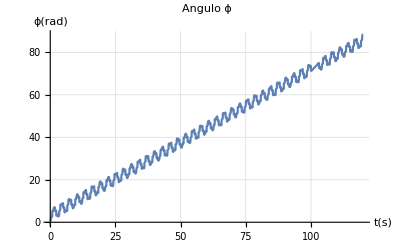

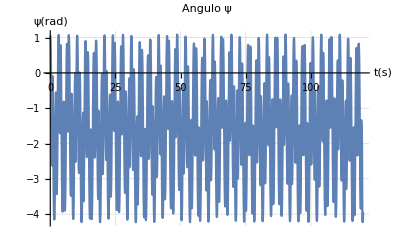

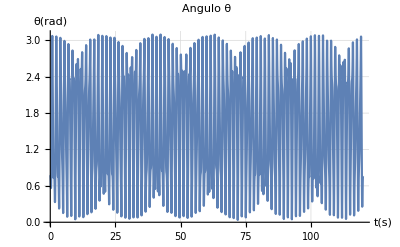

```mathematica
Plot[ϕsol[t],{t,0,120},AxesLabel->{"t(s)","ϕ(rad)"},LabelStyle->"Text", PlotLabel->Style["Angulo ϕ",FontSize->18,Black,Bold], GridLines->Automatic]
Plot[ψsol[t],{t,0,120},AxesLabel->{"t(s)","ψ(rad)"},LabelStyle->"Text", PlotLabel->Style["Angulo ψ",FontSize->18,Black,Bold], GridLines->Automatic]
Plot[θsol[t],{t,0,120},AxesLabel->{"t(s)","θ(rad)"},LabelStyle->"Text", PlotLabel->Style["Angulo θ",FontSize->18,Black,Bold], GridLines->Automatic]
```

Graficamos el momento angular en z en función del tiempo

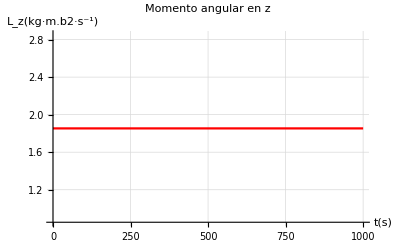

```mathematica
lz= I3 (fϕ(1+ (Sin[θsol[t]])^2)+fψ Cos[θsol[t]]);
Plot[lz,{t,0,1000},PlotRange->{{0,1000},{(lz /. t-> 456) -1,(lz /. t-> 456) +1}},AxesLabel->{"t(s)","L_z(kg·m.b2·s^-1)"},LabelStyle->"Text", PlotLabel->Style["Momento angular en z",FontSize->18,Black,Bold], GridLines->Automatic,PlotStyle->Red]
```

Graficamos la Energía en función del tiempo

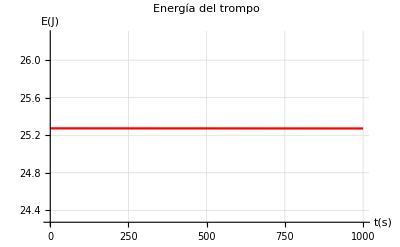

```mathematica
En= I3 (fθ^2 + fϕ^2 (Sin[θsol[t]])^2)+0.5I3(fψ+fϕ Cos[θsol[t]])^2 + m g d Sin[θsol[t]] Sin[ψsol[t]];
Plot[En,{t,0,1000},PlotRange->{{0,1000},{(En /. t-> 456) -1,(En /. t-> 456) +1}},AxesLabel->{"t(s)","E(J)"},LabelStyle->"Text",PlotLabel->Style["Energía del trompo",FontSize->18,Black,Bold], GridLines->Automatic,PlotStyle->Red]
```

Graficamos la constante de Kovalevskaya en función del tiempo

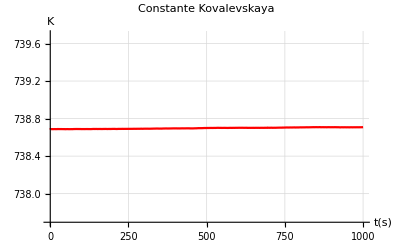

```mathematica
K= (fθ^2 + fϕ^2 (Sin[θsol[t]])^2)^2+ 2 m g d Sin[θsol[t]] ((fθ^2 - fϕ^2 (Sin[θsol[t]])^2)Sin[ψsol[t]]-2fθ  fϕ Sin[θsol[t]] Cos[ψsol[t]])/I3 + (m g d /I3)^2 (Sin[θsol[t]])^2 ;
Plot[K,{t,0,1000}, PlotRange->{{0,1000},{(K /. t-> 456) -1,(K/. t-> 456) +1}},AxesLabel->{"t(s)","K"},LabelStyle->"Text", PlotLabel->Style["Constante Kovalevskaya",FontSize->18, Black,Bold], GridLines->Automatic, PlotStyle->Red]
```

Como vemos en las tres gráficas anteriores para el trompo de Kovalevskaya se conserva el momento angular en z, la energía y la constante de Kovalevskaya  a lo largo del tiempo.

Referencias
[1] L. D. Landau and E. M. Liftshitz, Mechanics, 3rd. Edition, Pergamon Press (1976). 
[2] E. T. Whittaker, A treatise on the analytical dynamics of particles and rigid bodies, 2nd. Edition, Cambridge University Press (1917)
[3] M. Cosenza, Mecánica Clásica, Universidad de los Andes (2016).